# Bitcoin Energy Estimates (DRAFT)

## Estimating the energy use of the bitcoin network using two different approaches.

by Steven Black
Project home: https://github.com/StevenBlack/bitcoin-energy-estimates
Updated: October 23 2023

## Introduction

Bitcoin mining uses a proof-of-work consensus mechanism. This is controversial for some people because that supposedly requires a lot of electrical energy. We see claims the bitcoin network “uses as much electricity as a small country”, or “requires as much electricity as Belgium, or Chile.”

This Mathematica notebook assessed those notions using the following approaches:

Presuming bitcoin mining is marginally profitable, how much electical energy can be funded that balances actual mining rewards over time?

Given the reported hashrate, how much energy would be required to achieve that?

This paper uses Canadian dollars, partly because that’s my fiat currency, and because Canada publishes particularly good statistics about electricity generation and costs.

### Background: bitcoin price, block rewards, and fees

Here we outline the major factors that play in the economics of bitcoin mining.

#### The bitcoin price right now

What is the current price of bitcoin in Canadian dollars?

```mathematica
Now
```

Tue 24 Oct 2023 00:10:18GMT-4

```mathematica
BTCPrice =CurrencyConvert[Quantity[1,"Bitcoin"],Quantity[1,"CanadianDollars"]]
```

42 897.58 C$

#### Bitcoin block rewards

Bitcoin miners are compensated with block rewards from blocks they successfully mine, plus all the transaction fees in that block. In the current epoch (2020 - 2024) the block reward is 6 1/4 BTC.

```mathematica
blockReward = Quantity[6.25,"BTC"]/Quantity[1,IndependentUnit["block"]]
```

6.25 ฿

#### Bitcoin transaction fees per block

ASSUMPTION: the average transaction fees paid to miners, per block, is 0.125 BTC, which is about 2% of the total mining reward for each block.

```mathematica
blockTransactionFees=Quantity[0.125,"BTC"]/Quantity[IndependentUnit["block"]]
```

0.125 ฿

Therefore, the total bitcoin paid to miners for an average block, denominated in bitcoin.

```mathematica
blockRewardPlusFees=(blockReward+blockTransactionFees)
```

6.375 ฿

#### The actual block rate

Historically the bitcoin block production rate is faster then the block time target (6 per hour, or 144 blocks per day).  Let's reckon an average block rate over a sample interval of blocks in the immediate past.

Let's look at the past 100,000 blocks. How many days did it take to produce the last 100,000 blocks?

```mathematica
blockchainSampleInterval = 100000;
sampleIntervalTime =Now - BlockchainBlockData[-blockchainSampleInterval]["Timestamp"]
```

682.269 days

Let's calculate the average block time for those 100,000 blocks.

```mathematica
blockTime=UnitConvert[sampleIntervalTime/blockchainSampleInterval,MixedUnit[{"Minutes","Seconds"}]]
```

9 49.4808

We can now calculate the actual block rate per hour, and per day

```mathematica
blockRate = Quantity[1,"Hours"]/Quantity[blockTime, "Hours"/IndependentUnit["block"]]
```

6.10707 block/h

```mathematica
blockRatePerDay = blockRate * Quantity[24,"Hours"/"Day"]
```

146.57 block/day

#### Total miner compensation, per hour

```mathematica
blockRewardPlusFeesPerHour=blockRewardPlusFees*blockRate
```

38.9326 ฿

#### Bitcoin price in Canadian dollars as a time series

Let's gather data on bitcoin price over the past sampleIntervalTime.

```mathematica
btcPriceOverTime=CurrencyConvert["Bitcoin","CanadianDollars",{Now - sampleIntervalTime,Now}];
```

Let's graph that bitcoin price over time.

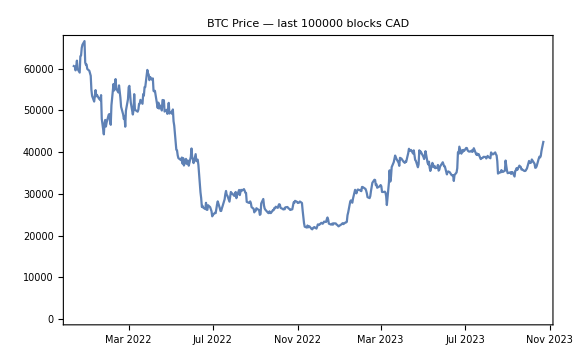

```mathematica
DateListPlot[
btcPriceOverTime,
PlotLabel->"BTC Price" <> "  — " <> "last " <> ToString[blockchainSampleInterval]<> " blocks\nCAD"
,FrameTicks->{Automatic,All}
,GridLines-> Automatic
,ImageSize->Large
]
```

#### Average bitcoin price over our sample time

```mathematica
btcPriceAvg=Mean[btcPriceOverTime]
```

36 939.31 C$

## 1. Assuming mining is ecomomically marginal, how much electricity could be funded by mining rewards?

### Global revenue per hour

The value, in Canadian Dollars, of all bitcoin mined globally, per hour.

```mathematica
blockCADperHour=Quantity[QuantityMagnitude[blockRewardPlusFeesPerHour], "per Hour"]* btcPriceAvg
```

1.43814×10^6 C$

### Electricity cost, per kWh

See: https://www.hydroquebec.com/business/customer-space/rates/comparison-electricity-prices.html

-Graphics-

Let’s presume that nobody in their right mind would want to mine bitcoin in New York or Boston. Here's the distribution of electricity input costs from the other 5 locations.

```mathematica
electricityInputCost = Quantity[
Around[
{0.0969,0.1042,0.1169,0.1365,0.1438}
]
,"CanadianDollars"
] /Quantity[1, "kWh"]
```

(0.1200.020) C$

### Business cost assumption

Let’s presume 85% of mining revenue is available to pay electricity cost. The rest covers wages, maintenance, depreciation, and taxes.

```mathematica
availableForElectricity = 0.85
```

0.85

### Economically sustainable mining power consumption

```mathematica
btcPower=(blockCADperHour*availableForElectricity)/electricityInputCost
```

1.020.1710^7 kW

Cognitively we can say, bitcoin's power consumption is in the order of 10 GWH.

### Economically sustainable mining energy consumption

```mathematica
AnnualEnergyConsumption = UnitConvert[
btcPower* Quantity[365*24,"Hours"] 
,"TWh"
]
```

(89.15.) h TW

Cognitively we can say, bitcoin's annual energy consumption is between 75 and 105 TWH.

### Comparisons with large power generation facilities or regions

Let’s compare the bitcoin network with the power and energy that generated, or used, by various things.

Here's the raw data for various generation facilities and regions.

```mathematica
generators = {
<|"name" -> "Robert-Bourassa generating station", "capacity"->Quantity[5616, "Megawatts"]|>
,<|"name" -> "Grand Coolee dam (USA)", "capacity"->Quantity[6809, "Megawatts"]|>
,<|"name" -> "Chile (2021)", "capacity"->Quantity[85, "Hours" "Terawatts"]/Quantity[365, "Days"]|>
,<|"name" -> "Belgium (2021)", "capacity"->Quantity[95, "Hours" "Terawatts"]/Quantity[365, "Days"]|>
,<|"name" -> "Three Gorges dam (China)", "capacity"->Quantity[22500, "Megawatts"]|>
,<|"name" -> "Province of Québec (2019)", "capacity"->Quantity[212.9, "Hours" "Terawatts"]/Quantity[365, "Days"]|>
,<|"name" -> "Canada (2021)", "capacity"->Quantity[626, "Hours" "Terawatts"]/Quantity[365, "Days"]|>
,<|"name" -> "USA (2021)", "capacity"->Quantity[4165, "Hours" "Terawatts"]/Quantity[365, "Days"]|>
,<|"name" -> "China (2021)", "capacity"->Quantity[8152, "Hours" "Terawatts"]/Quantity[365, "Days"]|>
,<|"name" -> "World (2021)", "capacity"->Quantity[27295, "Hours" "Terawatts"]/Quantity[365, "Days"]|>
};
```

```mathematica
Grid[
Prepend[
Table[
{#name,btcPower/#capacity}&[generators[[x]]]
,{x,1,Length[generators]}
]
,{"Facility or region", "BTC relative consumption"}
]
,Frame->All
]
```

Facility or region | BTC relative consumption
Robert-Bourassa generating station | (1.820.31) 
Grand Coolee dam (USA) | (1.500.25) 
Chile (2021) | (1.050.18) 
Belgium (2021) | (0.940.16) 
Three Gorges dam (China) | (0.450.08) 
Province of Québec (2019) | (0.420.07) 
Canada (2021) | (0.1430.024) 
USA (2021) | (0.0210.004) 
China (2021) | (0.01100.0019) 
World (2021) | (0.00330.0006)

## 2. Given the reported hashrate, how much energy would be required to achieve that?

Coming soon.

## Conclusion

The claims that  the bitcoin network “uses as much electricity as a small country”, or “requires as much electricity as Belgium, or Chile” seem reasonable from the perspectibe of bitcoin mining economics.

## Appendix

### Robert-Bourassa generating station — a.k.a. “LG-2”

Here we compare the power consumption of the bitcoin network with the power generation capacity of the Robert Bourassa generating station in the James Bay region of northern Québec. 
See https://en.wikipedia.org/wiki/Robert-Bourassa_generating_station

```mathematica
RobertBourassaDam = Quantity[5616, "Megawatts"]//UnitSimplify//N
```

5.616 GW

What is bitcoin’s global energy use in terms of LG-2?

```mathematica
btcPower/RobertBourassaDam
```

(1.820.31)

### Province of Québec

In 2019 the Province of Québec produced 212.9 TWh of electricity.

What is bitcoin’s global energy use as a proportion of Québec’s electricity production in 2019?

```mathematica
Québec2019=Quantity[212.9, "Hours" "Terawatts"]
```

212.9 h TW

```mathematica
Québec2019day=Québec2019/Quantity[365, "Days"]//UnitSimplify
```

24.3037 GW

```mathematica
btcPower /Québec2019day
```

(0.420.07)

### Province of Ontario

See https://www.cer-rec.gc.ca/en/data-analysis/energy-markets/provincial-territorial-energy-profiles/provincial-territorial-energy-profiles-ontario.html

In 2019, the average annual power consumption per capita in Ontario was 9.6 megawatt-hours (MWh).

```mathematica
Ontario2019PerCapita = Quantity[9.6,"Hours"*"Megawatts"/"People"]/Quantity[24*365,"Hours"];
Ontario2019PerCapita = UnitConvert[Ontario2019PerCapita,Quantity[, "Kilowatts"]/Quantity[, "People"]]
```

1.09589 kW/person

```mathematica
(btcPower/Ontario2019PerCapita)
```

9.31.610^6 people

### United States

See https://www.worlddata.info/america/usa/energy-consumption.php

```mathematica
USAPerCapita = Quantity[11.757,"Hours"*"Megawatts"/"People"]/Quantity[24*365,"Hours"];
USAPerCapita = UnitConvert[USAPerCapita,Quantity[, "Kilowatts"]/Quantity[, "People"]]
```

1.34212 kW/person

```mathematica
(btcPower/USAPerCapita)
```

7.61.310^6 people

### Europe

Again see See https://www.worlddata.info/america/usa/energy-consumption.php

```mathematica
EuropePerCapita = Quantity[5.462,"Hours"*"Megawatts"/"People"]/Quantity[24*365,"Hours"];
EuropePerCapita = UnitConvert[EuropePerCapita,Quantity[, "Kilowatts"]/Quantity[, "People"]]
```

0.623516 kW/person

```mathematica
(btcPower/EuropePerCapita)
```

1.640.2810^7 people